# Les polynômes orthogonales

## Formule de Rodrigues - Les polynômes de Jacobi P_n^(ν,μ)(x)

```mathematica
Clear["Global`*"]
```

Les polynômes de Jacobi, notés P_n^(ν,μ)(x)forment une suite de polynômes, P_0^(ν,μ)(x),P_1^(ν,μ)(x),P_2^(ν,μ)(x),...,P_k^(ν,μ)(x). Dans cette notation k est le nombre des polynômes qu'on veut les dériver et ν>-1 est un nombre réel .

```mathematica
k:=3
```

```mathematica
ν:=0
```

```mathematica
μ:=0
```

## Formule de Rodrigues

Les polynômes de Laguerre peut être définie par la formule de Rodrigues :

```mathematica
P[n_,ν_,μ_,x_]:=1/(Subscript[K, n] w[x])D[(w[x] s[x]^n), {x,n}]
```

### Initiation

```mathematica
table:=({{"Un polynôme de degrée 0, 1, ou 2", "s[x]", s[x_]=1-x^2}, {"Fonction poids", "w[x]", w[x_]=(1-x)^ν(1+x)^μ}, {"Limite gauche d'intervalle d'orthogonalité", "a", a=-1}, {"Limite droite d'intervalle d'orthogonalité", "b", b=+1}, {"Multiplicateur de standardisation", "K_n", Subscript[K, n_]=(-1)^n 2^n n!}, {"Définition du nombre d'Euler", "e", e=ⅇ}, {"Coefficient de x", "k_n", Subscript[k, n_]=Gamma[2n+ν+μ+1]/(2^n n!Gamma[n+ν+μ+1])}, {"Coefficient de x", "k'_n", Subscript[kp, n_]=(n(ν-μ))/(2n+ν+μ)Subscript[K, n]}, {"Carré de la norme", "I_n", Subscript[I, n_]=(2^(ν+μ+1)Gamma[n+ν+1]Gamma[n+μ+1])/((2n+ν+μ+1)n!Gamma[n+ν+μ+1])}, {"α_n dans la relation de récourence", "α_n", Subscript[α, n_]=Subscript[k, n+1]/Subscript[k, n]}, {"β_n dans la relation de récourence", "β_n", Subscript[β, n_]=Subscript[k, n+1]/Subscript[k, n](Subscript[kp, n+1]/Subscript[k, n+1]-Subscript[kp, n]/Subscript[k, n])}, {"γ_n dans la relation de récourence", "γ_n", Subscript[γ, n_]=-Subscript[I, n]/Subscript[I, n-1](Subscript[α, n]/Subscript[α, n-1])}, {"λ_n dans  l' équation différntiel ", "λ_n", Subscript[λ, n_]=n(Subscript[K, 1] D[P[1,ν,μ,x],x]+1/2(n-1)D[s[x], {x,2}])}})
```

### Tableau

```mathematica
Grid[table//FullSimplify,Frame->All]
```

Un polynôme de degrée 0, 1, ou 2 | s[x] | 1-x^2
Fonction poids | w[x] | 1
Limite gauche d'intervalle d'orthogonalité | a | -1
Limite droite d'intervalle d'orthogonalité | b | 1
Multiplicateur de standardisation | K_n | (-2)^n n!
Définition du nombre d'Euler | e | ⅇ
Coefficient de x | k_n | (2^-n Gamma[1+2 n])/Gamma[1+n]^2
Coefficient de x | k'_n | 0
Carré de la norme | I_n | 2/(1+2 n)
α_n dans la relation de récourence | α_n | 2-1/(1+n)
β_n dans la relation de récourence | β_n | 0
γ_n dans la relation de récourence | γ_n | -1+1/(1+n)
λ_n dans  l' équation différntiel  | λ_n | -n (1+n)

## Les polynômes

```mathematica
TableForm[Table[{n,P[n,ν,μ,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P[n,ν,μ,x]"}}]
```

n | P[n,ν,μ,x]
0 | 1
1 | x
2 | 1/2 (-1+3 x^2)
3 | 1/2 x (-3+5 x^2)

## Relation de récourence

Les polynômes de Laguerre satisfait la suite récurrente suivante :

```mathematica
"P_(n + 1)^(ν, μ)(x)"==( Subscript[α, n] x+Subscript[β, n])"P_n^(ν, μ)(x)"+Subscript[γ, n]"P_(n - 1)^(ν, μ)(x)"//FullSimplify
```

P_(n + 1)^(ν, μ)(x)==(-P_(n - 1)^(ν, μ)(x) n+P_n^(ν, μ)(x) (1+2 n) x)/(1+n)

## Orthogonalité

```mathematica
Table[∫_a^b w[x]P[n,ν,μ,x]P[n',ν,μ,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

2 | 0 | 0 | 0
0 | 2/3 | 0 | 0
0 | 0 | 2/5 | 0
0 | 0 | 0 | 2/7

```mathematica
Table[Subscript[I, n] KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

2 | 0 | 0 | 0
0 | 2/3 | 0 | 0
0 | 0 | 2/5 | 0
0 | 0 | 0 | 2/7

## Normalization

```mathematica
P̃[n_,ν_,μ_,x_]:=P[n,ν,μ,x]/(√Subscript[I, n])
```

```mathematica
TableForm[Table[{n,P̃[n,ν,μ,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P̃[n,ν,μ,x]"}}]
```

n | P̃[n,ν,μ,x]
0 | 1/(√2)
1 | √(3/2) x
2 | 1/2 √(5/2) (-1+3 x^2)
3 | 1/2 √(7/2) x (-3+5 x^2)

## Orthonormalité

```mathematica
Table[∫_a^b w[x]P̃[n,ν,μ,x]P̃[n',ν,μ,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
Table[KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## Développement de la fonction f(x)

### La fonction à développer

```mathematica
f[x_] := Abs[x]
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=∫_a^b w[x]P̃[n,ν,μ,x]f[x]ⅆx
```

```mathematica
Table[Subscript[a, n],{n,0,k}]
```

{1/(√2),0,(√(5/2))/4,0}

### Développement

```mathematica
fdev[x_]:=∑_(n=0)^5 Subscript[a, n] P̃[n,ν,μ,x]
```

## Représentation

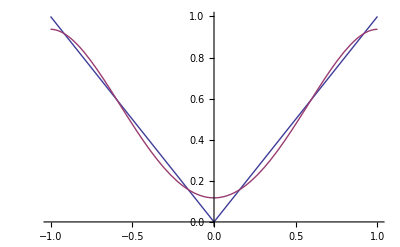

```mathematica
Plot[Evaluate[{f[x],fdev[x]}],{x,-1,1},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^k Subscript[a, n] P̃[n,ν,μ,x]}],{x,-1,1},PlotRange->All],{k,1,10,1},ControlType->Setter]
```

## EDP

Le n - ième polynôme de Laguerre satisfait l' équation différentielle suivante :

```mathematica
EDP=(D[(w[x] s[x]D[u[x], x]), x]-Subscript[λ, n] w[x]u[x])/w[x]==0//FullSimplify
```

n (1+n) u[x]==2 x u'[x]+(-1+x^2) u''[x]

```mathematica
DSolve[EDP,u[x],x]
```

{{u[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}}

```mathematica
TableForm[Table[{n,P[n,ν,μ,x],JacobiP[n,ν,μ,x],LegendreP[n,x],GegenbauerC[n,λ,x],ChebyshevT[n,x],ChebyshevU[n,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,2},TableHeadings->{None,{"n","P[n,ν,μ,x]","JacobiP[n,ν,μ,x]","LegendreP[n,x]","GegenbauerC[n,λ,x]","ChebyshevT[n,x]","ChebyshevU[n,x]"}}]
```

n | P[n,ν,μ,x] | JacobiP[n,ν,μ,x] | LegendreP[n,x] | GegenbauerC[n,λ,x] | ChebyshevT[n,x] | ChebyshevU[n,x]
0 | 1 | 1 | 1 | 1 | 1 | 1
1 | x | x | x | 2 x λ | x | 2 x
2 | 1/2 (-1+3 x^2) | 1/2 (-1+3 x^2) | 1/2 (-1+3 x^2) | λ (-1+2 x^2 (1+λ)) | -1+2 x^2 | -1+4 x^2
3 | 1/2 x (-3+5 x^2) | 1/2 x (-3+5 x^2) | 1/2 x (-3+5 x^2) | 2/3 x λ (1+λ) (-3+2 x^2 (2+λ)) | x (-3+4 x^2) | -4 x+8 x^3